## Mathieu-Hill Equations BSA, 2024

```mathematica
ClearAll["Global`*"]
```

### Initial Data

```mathematica
n = 5;
k = 2;
```

```mathematica
Eq = x''[t] + (δ + ϵ * Cos[t]) * x[t] == 0
```

(δ+ϵ Cos[t]) x[t]+x''[t]==0

### Hill Determinants

```mathematica
ComputeA1[δ_, ϵ_, n_] := Table[If[i == j, δ - (i - 1)^2, If[i == 1 && j == 2, ϵ, If[Abs[i - j] == 1, ϵ / 2, 0]]], {i, n}, {j, n}];
ComputeA2[δ_, ϵ_, n_] := Table[If[i == j, δ - i^2, If[Abs[i - j] == 1, ϵ / 2, 0]], {i, n}, {j, n}];
ComputeA3[δ_, ϵ_, n_] := Table[If[i == 1 && j == 1, δ - 1/4 + ϵ / 2, If[i == j, δ - (2 * i - 1)^2 / 4, If[Abs[i - j] == 1, ϵ / 2, 0]]], {i, n}, {j, n}];
ComputeA4[δ_, ϵ_, n_] := Table[If[i == 1 && j == 1, δ - 1/4 - ϵ / 2, If[i == j, δ - (2 * i - 1)^2 / 4, If[Abs[i - j] == 1, ϵ / 2, 0]]], {i, n}, {j, n}];
```

```mathematica
F[δ_, ϵ_, n_] := Det[ComputeA1[δ, ϵ, n]] * Det[ComputeA2[δ, ϵ, n]] * Det[ComputeA3[δ, ϵ, n]] * Det[ComputeA4[δ, ϵ, n]];
```

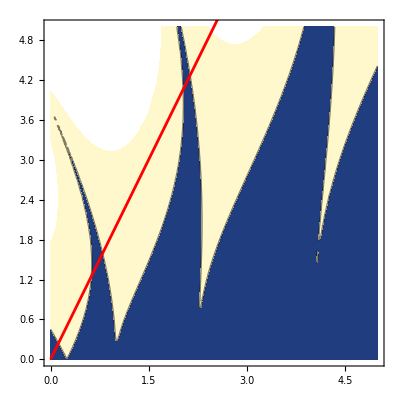

```mathematica
p1 = ContourPlot[F[δ, ϵ, n], {δ, 0, 5}, {ϵ, 0, 5}, Contours -> {0}, PlotPoints -> 20];
p2 = Plot[k * δ, {δ, 0, 5}, PlotStyle->Red];
Show[p1, p2]
```

### Stability Intervals

```mathematica
SolDelta = Flatten[NSolve[{F[δ, k * δ, n], -0.1 < δ < 3}, δ]]
```

{δ→0,δ→0.121527,δ→0.623819,δ→0.796839,δ→2.02718,δ→2.13548}

```mathematica
StabInt = Table[{SolDelta[[i, 2]], SolDelta[[i + 1, 2]]}, {i, 1, Length[SolDelta], 2}]
```

{{0,0.121527},{0.623819,0.796839},{2.02718,2.13548}}

### Plot Solution

```mathematica
PlotSol[δi_, ϵi_, L_, i_] := (
	X = NDSolve[{Eq /. {δ -> δi, ϵ -> ϵi}, x[0] == 0, x'[0] == 0.1}, x[t], {t, 0, L}][[1]][[1, 2]];
	p1 = Plot[X, {t, 0, L}, GridLines -> Automatic, AxesLabel -> {t, x[t]}, PlotRange -> All, PlotLabel->Style[Round[StabInt[[i, All]], 0.0001], 10], 
		ImageSize->Scaled[0.8], AspectRatio -> 1];
	p2 = Show[ContourPlot[F[δ, ϵ, n], {δ, 0, 5}, {ϵ, 0, 5}, Contours -> {0}, PlotPoints -> 20, ImageSize -> Scaled[0.7]], 
		Plot[k * δ, {δ, 0, 5}, PlotStyle->Red], Graphics[{Yellow, PointSize[Large], Point[{δi, ϵi}]}]];
	GraphicsRow[{p1, p2}]
);
```

```mathematica
Manipulate[Manipulate[PlotSol[δ, k * δ, 80, i], {δ, StabInt[[i, 1]] - 0.01, StabInt[[i, 2]] + 0.01, Appearance -> "Open"}], {i, {1, 2, 3}}]
```